```mathematica
SetDirectory@NotebookDirectory[]
```

C:\Users\79636\Desktop\Сириус\integrator-main\build

```mathematica
data=Import["sph11000.dat","Table"]
```

{{5663,11385},17047,{11385,203,5617,5658,5659}}
 |  |  |  |

```mathematica
np=data[[1,1]]
```

5663

```mathematica
nc=data[[1,2]]
```

11385

```mathematica
pts=data[[2;;1+np]][[All,2;;]];
```

```mathematica
topoAll=data[[2+np;;]]
```

{{1,102,1,3},{2,102,3,4},{3,102,4,5},11380,{11384,203,5614,5651,5654},{11385,203,5617,5658,5659}}
 |  |  |  |

```mathematica
topo=Cases[topoAll,{_,203,x__}:>{x}]
```

{{1,3,65},{4,5,66},{6,7,67},{8,9,68},11315,{5624,5655,5659},{5614,5651,5654},{5617,5658,5659}}
 |  |  |  |

```mathematica
Length@topo
```

11322

```mathematica
trg[i_]:=Triangle[pts[[topo[[i]]]]]
```

```mathematica
Show[Graphics3D[Table[trg[i],{i,Length@topo}],Boxed->False](*,Graphics3D[{Red,trg[10935],trg[10958]}]*)(*,Graphics3D[Ball[Mean@pts[[topo[[5417]]]],1000]]*),Framed->False]
```

-Graphics3D-

```mathematica
Graphics3D[{trg[10935],trg[10958]}]
```

-Graphics3D-

```mathematica
topo[[10935]]
```

{5460,5501,5491}

```mathematica
topo[[10958]]
```

{5501,5469,5560}

```mathematica
pts[[{4773,4719,4774,4720}]]
```

{{-0.966268,-0.00786134,-0.257419},{0.233916,0.958824,-0.161058},{-0.827291,-0.492364,0.270494},{0.000337672,0.934198,0.356754}}

```mathematica
{{0.980029385876598,-0.00286558266991517,0.5},{0.990015988053133,0.00144181708948758,0.5},{0.990015988053134,-0.00144181708948759,0.5},{0.980029385876598,0.00286558266991515,0.5}}
```

{{0.980029,-0.00286558,0.5},{0.990016,0.00144182,0.5},{0.990016,-0.00144182,0.5},{0.980029,0.00286558,0.5}}

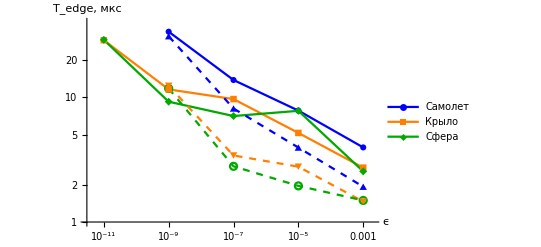

```mathematica
figEdge=ListLogLogPlot[{Legended[{{10^-9,3.37*10^1},{10^-7,1.38*10^1},{10^-5,7.84*10^0},{10^-3,3.97*10^0}},"Самолет"],Legended[{{10^-11,2.88*10^1},{10^-9,1.16*10^1},{10^-7,9.7*10^0},{10^-5,5.19*10^0},{10^-3,2.73*10^0}},"Крыло"],Legended[{{10^-11,2.9*10^1},{10^-9,9.24*10^0},{10^-7,7.09*10^0},{10^-5,7.81*10^0},{10^-3,2.55*10^0}},"Сфера"],
{{10^-9,3.1*10^1},{10^-7,8.15*10^0},{10^-5,3.96*10^0},{10^-3,1.92*10^0}},
{{10^-9,1.24*10^1},{10^-7,3.42*10^0},{10^-5,2.78*10^0},{10^-3,1.46*10^0}},{{10^-9,1.18*10^1},{10^-7,2.8*10^0},{10^-5,1.95*10^0},{10^-3,1.49*10^0}}},
PlotStyle->{Blue,Orange,Darker@Green,Directive[Blue,Dashed],Directive[Orange,Dashed],Directive[Darker@Green,Dashed]},
Joined->True,PlotMarkers->Automatic,Ticks->{{{10^-11,"10^-11"},{10^-9,"10^-9"},{10^-7,"10^-7"},{10^-5,"10^-5"},{10^-3,"10^-3"}},Automatic},AxesLabel->{"ϵ","T_edge, мкс"},LabelStyle->Directive[16,Black,FontFamily->"Times"],GridLines->{{10^-11,10^-9,10^-7,10^-5,10^-3},{2,5,10,20,40}},GridLinesStyle->Directive[Black, Thickness[0.002],Dashed],PlotRange->{{3 10^-12,2 10^-3},{1,40}}]
```

```mathematica
Export["figEdge.pdf",figEdge]
```

figEdge.pdf

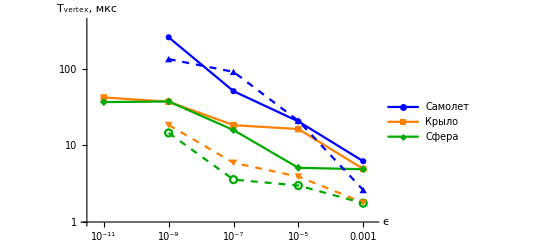

```mathematica
figVertex=ListLogLogPlot[{Legended[{{10^-9,2.56*10^2},{10^-7,5.08*10^1},{10^-5,2.05*10^1},{10^-3,6.2*10^0}},"Самолет"],Legended[{{10^-11,4.21*10^1},{10^-9,3.7*10^1},{10^-7,1.83*10^1},{10^-5,1.63*10^1},{10^-3,4.92*10^0}},"Крыло"],Legended[{{10^-11,3.66*10^1},{10^-9,3.73*10^1},{10^-7,1.58*10^1},{10^-5,5.09*10^0},{10^-3,4.88*10^0}},"Сфера"],
{{10^-9,1.33*10^2},{10^-7,9.07*10^1},{10^-5,2.09*10^1},{10^-3,2.61*10^0}},
{{10^-9,1.84*10^1},{10^-7,5.91*10^0},{10^-5,3.91*10^0},{10^-3,1.79*10^0}},{{10^-9,1.45*10^1},{10^-7,3.57*10^0},{10^-5,2.99*10^0},{10^-3,1.76*10^0}}},
PlotStyle->{Blue,Orange,Darker@Green,Directive[Blue,Dashed],Directive[Orange,Dashed],Directive[Darker@Green,Dashed]},
Joined->True,PlotMarkers->Automatic,Ticks->{{{10^-11,"10^-11"},{10^-9,"10^-9"},{10^-7,"10^-7"},{10^-5,"10^-5"},{10^-3,"10^-3"}},Automatic},AxesLabel->{"ϵ","T_vertex, мкс"},LabelStyle->Directive[16,Black,FontFamily->"Times"],GridLines->{{10^-11,10^-9,10^-7,10^-5,10^-3},{2,5,10,20,50,100,200}},GridLinesStyle->Directive[Black, Thickness[0.002],Dashed],PlotRange->{{3 10^-12,2 10^-3},{1,400}}]
```

```mathematica
Export["figVertex.pdf",figVertex]
```

figVertex.pdf